## Harvest model with Type III response - single trajectories - short time

## Setup and Universal Parameters

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fold_harvest/figures"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* get package for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Universal simulation parameters *)
dt=0.1; (* time step for stochastic simulation *)
dt2 = 1; (* time separation for indicator calculation - increase to speed up computation *)
tmax=400 ; (* max time in simulation *)
numSims=3; (* number of realisations to average over *)

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)
toffset=0; (* time before bifurcation point to stop evaluating EWS *)

(* hamming window size and length *)
hamLength=20; 
hamOffset=5; 


(* lag autocorrelation *)
numComps=tmax/dt+1; (* number of components in simulation *)
tauVals={1,2};

(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.10}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
```

## Model Analysis

Use bistable harvesting model : dx/dt = rx(1-x) - hx^2/(s^2 +x^2)

```mathematica
(* Clear variable names *)
Clear[f,x,r,h,s]
$Assumptions={x,r,a,s}∈Reals;
```

```mathematica
(* Dynamic equations *)
f[x_]:=r x(1-x) - h x^2/(s^2+x^2);
```

```mathematica
f[x]
```

r (1-x) x-(h x^2)/(s^2+x^2)

```mathematica
(* Parameter values *)
r=1;
s=0.1;
```

```mathematica
(* Find equilibiria *)
equi=Solve[f[x]==0,x]//Quiet;
```

```mathematica
equi/.{h->0.1}
```

{{x→0.},{x→0.0555458+0.0903572 ⅈ},{x→0.888908+0. ⅈ},{x→0.0555458-0.0903572 ⅈ}}

```mathematica
(* Initial stable equilibrium *)
equiInit=Re[x/.equi[[3]]];

(* Bifurcation point *)
{xbif,hbif}=Re[{x,h}/.Solve[f[x]==0&&f'[x]==0][[3]]]//Quiet
```

{0.478128,0.260437}

```mathematica
(* Eigenvalue at equilibrium point *)
Clear[λ]
λ[a_]=D[f[x],x]/.{x->equiInit};
```

```mathematica
(* Phase portrait, hval control parameter *)
Manipulate[
Plot[f[x]/.{r->rval,h->hval,s->sval},{x,0,1},
PlotRange->{-0.2,0.2},
AxesLabel->{"x","f(x)"},
LabelStyle->TMBFS12],
{{rval,1},0.5,1.5},{{hval,0},0,0.4},{{sval,0.1},0.05,0.3}];
```

## Stochastic Simulation

Stochastic model 
dX = rX(1-X) -hX^2/(s^2+X^2)

### Key parameters

```mathematica
a1=0.02;(* noise intensity *)
r=1; (* model parameteres *)
s=0.1;
hl=0.15; (* min value of control parameter *)
hh=0.28; (* max value of control parameter *)
x0=equiInit/.h->hl; (* initial condition *)
seed=10; (* seed number *)

(* lag autocorrelation *)
numComps=tmax/dt+1;
tauVals={1,2};
```

### Model Dynamics

```mathematica
Clear[f]
f[x_,h_]:=r x(1-x)-h x^2/(s^2+x^2);
```

### Stochastic Simulation

```mathematica
(* clear function labels *)
Clear[stochProc,stochSol,stochData]
```

```mathematica
(* evolution of control param - harvesting rate *)
Clear[h,t]
h[t_]:=((hh-hl)/tmax) t +hl
```

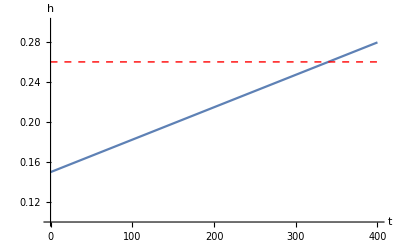

```mathematica
(* Critical time *)
tcrit=t/.Solve[h[t]==hbif,t][[1]];

(* h plot *)
hPlot=Plot[{h[t],hbif},{t,0,tmax},
LabelStyle->14,
AxesLabel->{"t","h"},
PlotStyle->{Automatic,{Dashed,Thick,Red}},
PlotRange->{{0,tmax},{0.1,0.3}}]
```

```mathematica
(* number of components in simulation *)
nComps=Floor[tmax/dt]+1;
```

```mathematica
(* array for output time-series *)
x=ConstantArray[0,{numSims,nComps}];
t=Range[0,tmax,dt];
```

```mathematica
(* intitial condition *)
x[[;;,1]]=x0;
```

```mathematica
(* noise values *)
noiseVals=RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
x[[j,i+1]]=x[[j,i]]+f[x[[j,i]],h[t[[i]]]]dt+a1*Sqrt[dt]*noiseVals[[j,i]];
(* make sure state variable stays above x=0 *)
If[x[[j,i+1]]≤0,x[[j,i+1]]=0];
]
]
```

```mathematica
(* dimensions of xVals - (num realisations, tstep)  *)
x//Dimensions
```

{3,4001}

```mathematica
(* assign *)
tValsFull=t;
xValsFull=x;
```

### Filter time-series to improve computation time

```mathematica
(* Filter time-series seperation of dt2 to make analysis computationally feasible *)
tVals=Take[tValsFull,{1,Length[tValsFull],dt2/dt}];
xVals=Take[xValsFull,All,{1,Length[tValsFull],dt2/dt}];
```

### Single realisation plots

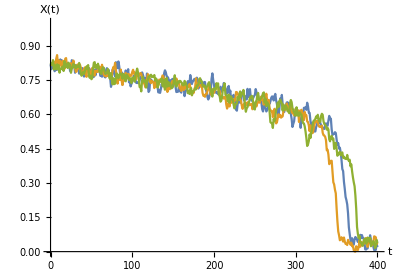

```mathematica
(* make plot of single realisation in x *)
plotX=ListPlot[Table[{tVals,xVals[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{{0,tmax},{0,1}},
AspectRatio->0.7]
```

## Traditional EWS

### Detrend - fit Gaussian

```mathematica
(* work with data only up to bifurcation (tcrit) minus 20 yrs *)
idxCrit=FirstPosition[tVals,t_/;t≥tcrit-toffset][[1]]-1;
tValsShort=tVals[[1;;idxCrit]];
```

```mathematica
dataFitX=If[detrendOp==1,
Table[GaussianFilter[xVals[[i,1;;idxCrit]],Length[tValsShort]*bandWidth],{i,1,numSims}],
ConstantArray[0,{numSims,idxCrit}]];
```

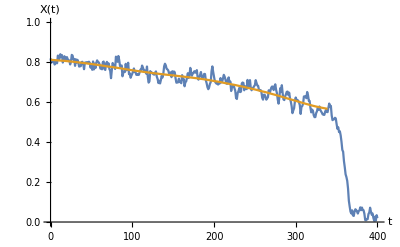

```mathematica
(* plot of a single X realisation fitted *)
fitPlotX=ListPlot[{{tVals,xVals[[1]]}ᵀ,{tValsShort,dataFitX[[1]]}ᵀ},
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{{0,tmax},{0,1}}]
```

### Residuals

```mathematica
residualsX=xVals[[;;,1;;idxCrit]]-dataFitX;
residualsX//Dimensions
```

{3,340}

```mathematica
(* plot of a single realisation *)
residPlotX=ListPlot[{tValsShort,residualsX[[1]]}ᵀ,
Joined->True,
Filling->Axis,
AxesLabel->{"t","Res"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All}];
```

### Variation of Residuals

```mathematica
(* number of components in rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
```

```mathematica
(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
varSeriesX=Table[MovingMap[Variance,residualsX[[i]],windowComps],{i,1,numSims}];
varSeriesX//Dimensions
```

{3,240}

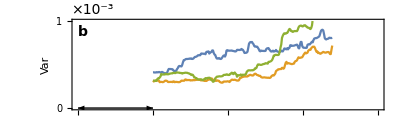

```mathematica
(* plot individual realisations *)
varPlotX=ListPlot[Table[{tValsShort[[windowComps+1;;]],varSeriesX[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.001}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{{{0,0},{0.0005,0.5},{0.001,1},{0.0015,1.5}},Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-3",14],indexPos],
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at lag 1

```mathematica
(* form [a1;a2;,,,;an] *)
acSeriesX=Table[MovingMap[CorrelationFunction[#,1]&,residualsX[[i]],windowComps],{i,1,numSims}];  
acSeriesX//Dimensions
(* sim number, lag number, time value *)
```

{3,240}

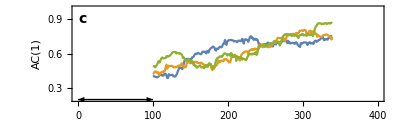

```mathematica
(* ac-1 plot of single realisations *)
acPlotX=ListPlot[Table[{tValsShort[[windowComps+1;;]],acSeriesX[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC(1)",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{0.2,1}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0.2 (* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,0.2 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

## Power Spectrum EWS

### Compute power spectrum over rolling window with same offset has Hamming windows

```mathematica
(* evaluate power spectrum of residuals in rolling window with the offset the same as hamOffset *)
pSpecSeriesX=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,residualsX[[i]],{windowComps,Left,hamOffset}],{i,1,numSims}];
```

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesX[[1,1,1]];
```

### Plot of individual realisations

```mathematica
pSpecSeriesX//Dimensions
```

{3,48,2,21}

```mathematica
tcrit
```

339.805

```mathematica
(* plot times to use *)
plotTimes=Range[dt2*windowComps,tcrit-50,hamOffset]
```

{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

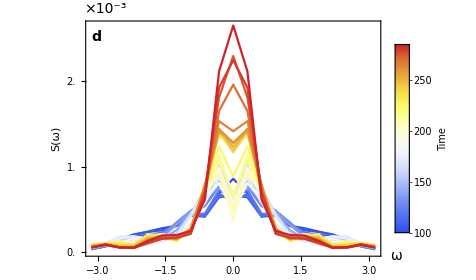

```mathematica
(* normalise to map to a colour *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
psdSinglePlot=ListLinePlot[Table[Transpose[pSpecSeriesX[[2,tindex]]],{tindex,1,Length[plotTimes]}],
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-3",14],Scaled[{0.065,1.05}]],
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,5,0.5]*10^(-3),Range[0,5,0.5]}],Automatic},{Automatic,Automatic}},
PlotLegends->Placed[colLegend,Scaled[{0.9,0.55}]]]
```

### Max-frequency component

```mathematica
pSpecSeriesX//Dimensions
```

{3,48,2,21}

```mathematica
(* Subscript[S, max] data *)
specMax=Table[Max[pSpecSeriesX[[i,j,2,;;]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX][[2]]}];
specMax//Dimensions
```

{3,48}

```mathematica
tValsShort[[windowComps+1;;-1;;hamOffset]]//Dimensions
```

{48}

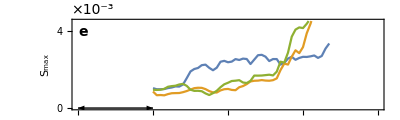

```mathematica
(* plot individual realisations *)
specMaxPlot=ListPlot[Table[{tValsShort[[windowComps+1;;-1;;hamOffset]],specMax[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.0045}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{Transpose[{10^(-3)*Range[0,10],Range[0,10]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-3",14],indexPos],
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### Hopf-AIC weight

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
pSpecSeriesX//Dimensions
```

{3,48,2,21}

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
Timing[TBFitSpec[pSpecSeriesX[[1,10]]]]
```

{0.238159,{1.,2.2115×10^-14,1.06861×10^-10}}

```mathematica
(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesX=Monitor[
Table[Quiet[TBFitSpec[pSpecSeriesX[[i,j]]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX]⟦2⟧}],
{ProgressIndicator[i,{1,numSims}],ProgressIndicator[j,{1,Dimensions[pSpecSeriesX]⟦2⟧}]}];
```

```mathematica
aicWeightSeriesX//Dimensions
```

{3,48,3}

```mathematica
pSpecSeriesX//Dimensions
```

{3,48,2,21}

```mathematica
(* plot of individual realisations for wfold *)
aicFoldPlot=ListPlot[Table[
{tValsShort[[windowComps+1;;-1;;hamOffset]],aicWeightSeriesX[[i,;;,1]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
PlotStyle->TMBcolours[[1]],
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameLabel->{{"w_fold",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}];
```

```mathematica
(* plot of individual realisations for whopf *)
aicHopfPlot=ListPlot[Table[
{tValsShort[[windowComps+1;;-1;;hamOffset]],aicWeightSeriesX[[i,;;,2]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotStyle->TMBcolours[[4]],
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{False,True},{False,False}},
FrameStyle->{Automatic,Automatic,Automatic,TMBcolours[[4]]},
FrameLabel->{{"","w_hopf"},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{None,Range[0,1,0.2]},{None,None}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3];
```

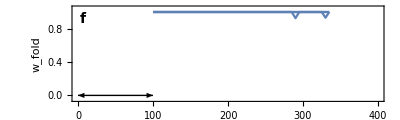
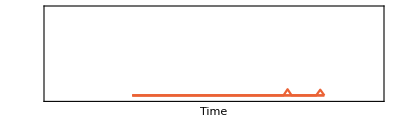

```mathematica
aicPlot=Overlay[{aicFoldPlot,aicHopfPlot}]
```

## Bifurcation diagram

### Specifications

```mathematica
(* Import data *)
rawdata=Import["../bifurcation_data/fold.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of mu *)
hbifVals=fulldata[[;;,1]];
tbifVals=(hbifVals-hl)*tmax /(hh-hl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections=Append[nodeSections,Cases[nodeSections[[7]],{_,x_,_,_}/;x<=0.75]];
nodeSections[[7]]=Cases[nodeSections[[7]],{_,x_,_,_}/; x>=0.65] ;*)(* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}];
```

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

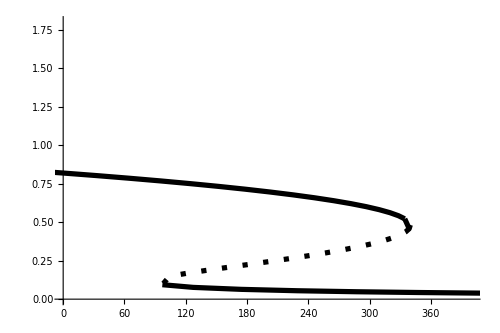

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,1.8}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

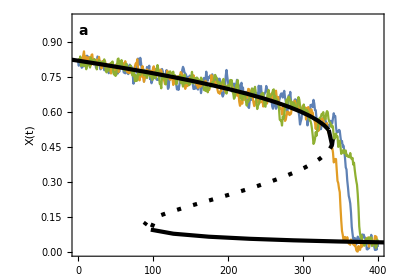

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajX=Show[{plotX,bifPlotNormal},
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"X(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
]
```

## Combined Plot

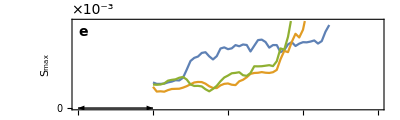
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
foldEwsPlot=Grid[{{bifTrajX,psdSinglePlot},{varPlotX,specMaxPlot},{acPlotX,aicPlot}},Spacings->{-2.5,0}]
```

```mathematica
(*Export["fold_harvest_trans_short.png",foldEwsPlot,ImageResolution->200];*)
```